# Neural ODE parametrization

## Integrals in original variables

### η-coordinate

In these coordinates, AdS_5-BH is

```mathematica
f[η_]:= Tanh[2η]Sinh[2η]
g[η_]:= Cosh[2η]
```

The integrals are

```mathematica
Clear[f,g]
```

```mathematica
L[ηs_]:=2NIntegrate[(√(f[ηs]g[ηs]))/(√g[η] √(f[η]g[η]-f[ηs]g[ηs])),{η,ηs,∞}]
V[ηs_]:=2NIntegrate[(f[η] √g[η])/(√(f[η]g[η]-f[ηs]g[ηs]))-√f[η],{η,ηs,10}]-2NIntegrate[√f[η],{η,0,ηs}]
```

```mathematica
√(f[η](g[η]+x^2))/.x->(√(f[ηs]g[ηs]))/(√g[η] √(f[η]g[η]-f[ηs]g[ηs]))//Simplify
```

√(f[η] (g[η]+(f[ηs] g[ηs])/(f[η] g[η]^2-f[ηs] g[η] g[ηs])))

```mathematica
%/.ηs->0
```

√(f[η] (g[η]+(f[0] g[0])/(-f[0] g[0] g[η]+f[η] g[η]^2)))

```mathematica
(f[η] √g[η])/(√(f[η]g[η]-f[ηs]g[ηs]))/.ηs->∞
```

(f[η] √g[η])/(√(-f[0] g[0]+f[η] g[η]))

The regularization is such that the disconnected phase always has V=0 regardless of f and g.

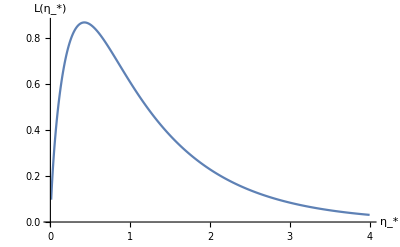

```mathematica
figL=ListLinePlot[Table[{ηs,L[ηs]},{ηs,0.01,4,0.01}],AxesLabel->{"η_*","L(η_*)"}]
```

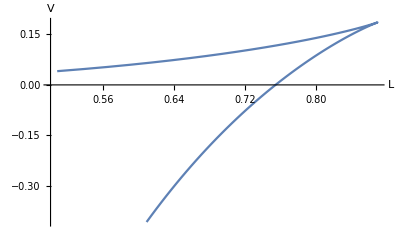

```mathematica
figV=ListLinePlot[Table[{L[ηs],V[ηs]},{ηs,0.1,1,0.01}],AxesLabel->{"L","V"}]
```

### z-coordinate

In this more conventional coordinate system, the metric is
d s^2=1/z^2(-f(z)d t^2+g(z)d z^2+d (x̄)^2) .
This time AdS_5-BH would be (with horizon set to z_h=1)

```mathematica
f[z_]:=1-z^4
g[z_]:=1/(1-z^4)
```

The connection between z<->η -coordinates is (in this AdS_5-BH case)

```mathematica
Solve[1-z^4==Cosh[2η],η]/.C[1]->0//FullSimplify
Solve[1/(1-z^4)==Cosh[2η],z]/.C[1]->0//FullSimplify
```

{{η→-1/2 ArcCosh[1-z^4]},{η→1/2 ArcCosh[1-z^4]}}

{{z→-(1-Sech[2 η])^(1/4)},{z→-ⅈ (1-Sech[2 η])^(1/4)},{z→ⅈ (1-Sech[2 η])^(1/4)},{z→(1-Sech[2 η])^(1/4)}}

```mathematica
Cosh[2η]/.η->(1-Sech[2 η])^(1/4)//FullSimplify
```

Cosh[2 (1-Sech[2 η])^(1/4)]

```mathematica
f[Sech[2η]]
```

1-Sech[2 η]^4

So
L=2∫_0^(z_*) (z^2 √(f(z_*)g(z)))/(√((z_*)^4 f(z)-z^4 f(z_*)))ⅆz 
V=2∫_0^(z_*) (√(f(z)g(z)))/z^2(1/(√(1-(z^4 f(z_*))/((z_*)^4 f(z))))-1)ⅆz-2∫_(z_*)^1 (√(f(z)g(z)))/z^2 ⅆz ,
where as regularization of V we have subtracted two straight strings which would contribute
V_(||)=2∫_ϵ^(z_*) (√(f(z)g(z)))/z^2 ⅆz .
This also has the effect that the connected-disconnected phase transition happens at V=0 for any f and g.

```mathematica
L[zs_]:=2NIntegrate[(z^2 √(f[zs]g[z]))/(√(zs^4 f[z]-z^4 f[zs])),{z,0,zs}]
V[zs_]:=2NIntegrate[(√(f[z]g[z]))/z^2(1/(√(1-(z^4 f[zs])/(zs^4 f[z])))-1),{z,0,zs}]-2NIntegrate[(√(f[z]g[z]))/z^2,{z,zs,1}]
```

```mathematica
Clear[f,g]
```

```mathematica
D[(z^2 √(f[zs]g[z]))/(√(zs^4 f[z]-z^4 f[zs])),zs]//FullSimplify
```

(z^2 zs^3 f[z] g[z] (-4 f[zs]+zs f'[zs]))/(2 (zs^4 f[z]-z^4 f[zs])^(3/2) √(f[zs] g[z]))

```mathematica
D[f[z],z]
```

-4 z^3

```mathematica
dL[z_,zs_]:=(z^2 zs^3 f[z] g[z] (-4 f[zs]-zs 4 zs^3))/(2 (zs^4 f[z]-z^4 f[zs])^(3/2) √(f[zs] g[z]));
```

```mathematica
Series[(z^2 zs^3 f[z] g[z] (-4 f[zs]-zs 4 zs^3))/(2 (zs^4 f[z]-z^4 f[zs])^(3/2) √(f[zs] g[z])),{z,0,10}]
```

-(2 zs^3 z^2)/((zs^4)^(3/2) √(1-zs^4))+1/2 zs^3 (3/(2 (zs^4)^(5/2) √(1-zs^4))-1/(2 (zs^4)^(3/2) √(1-zs^4))) (-4 zs^4-4 (1-zs^4)) z^6+1/2 zs^3 (-3/(4 (zs^4)^(5/2) √(1-zs^4))-1/(8 (zs^4)^(3/2) √(1-zs^4))+15/(8 zs^8 (zs^4)^(3/2) √(1-zs^4))) (-4 zs^4-4 (1-zs^4)) z^10+O[z]^11

what it is in the code: (old)

dL integrand  = -4 - 2z g’(z) + 4 zs^4 f(z)/(z^4 f(zs)) - 2(zs^4 f(z)f'(z))/(z^3 f(zs))+2 zs^5 f'(zs)(f(z))/(z^4 f(zs))+2 zs^4 g'(z)(f(z))/(z^3 f(zs))

```mathematica
D[f[z],z]
```

-4 z^3

```mathematica
D[g[z],z]
```

(4 z^3)/((1-z^4)^2)

```mathematica
olddL[z_,zs_]:=(-√g[z])/(((zs^4 f[z])/(z^4 f[zs])-1)^(3/2))(-4-2z(4 z^3)/((1-z^4)^2)+4 zs^4 f[z]/(z^4 f[zs])-(2 zs^4 f[z](-4 z^3))/(z^3 f[zs])+2 zs^5(-4 z^3)f[z]/(z^4 f[zs])+2 zs^4(4 z^3)/((1-z^4)^2)f[z]/(z^3 f[zs]));
```

```mathematica
dL[0.25,0.5]
```

-1.13555

```mathematica
dL2[z_,zs_]:=(z^4 zs^3 f[z] √(-1+(zs^4 f[z] g[z])/(z^4 f[zs] g[zs])) (zs g[zs] (-4 zs^3)+f[zs] (-4 g[zs]+zs (4 zs^3)/((1-zs^4)^2))))/(2 (zs^4 f[z] g[z]-z^4 f[zs] g[zs])^2)
```

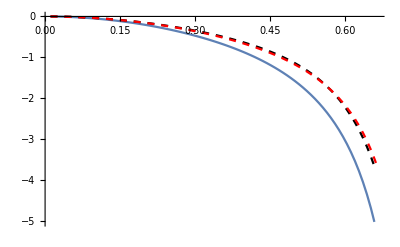

```mathematica
Show[ListLinePlot[Table[{z,dL[z,0.8]},{z,gridzs}]],ListLinePlot[Table[{z,0.8olddL[z,0.8]},{z,gridzs}],PlotStyle->{Black,Dashed}],ListLinePlot[Table[{z,dL2[z,0.8]},{z,gridzs}],PlotStyle->{Red,Dashed}],PlotRange->All]
```

Width w.r.t. z_*

```mathematica
Clear[f,g]
```

CHECKING :

```mathematica
(zs-1)1/(√g[z] √((zs^4 f[z]g[z])/(z^4 f[zs]g[zs])))/.z->1-y+y zs//FullSimplify
```

(-1+zs)/(√g[1+y (-1+zs)] √((zs^4 f[1+y (-1+zs)] g[1+y (-1+zs)])/((1+y (-1+zs))^4 f[zs] g[zs])))

```mathematica
Clear[f,g]
```

THERE ARE THE COORDINATES TO GO WITH, NOTE REGURALIZATION

```mathematica
L2[zs_]:=2NIntegrate[(z^2 √(f[zs]g[zs]))/(g[z] √(zs^4 f[z]g[z]-z^4 f[zs]g[zs])),{z,0,zs}]
V2[zs_]:=2NIntegrate[(√f[z])/z^2(1/(√g[z] √(1-(z^4 f[zs]g[zs])/(zs^4 f[z]g[z])))-1),{z,0,zs}]-2NIntegrate[(√f[z])/z^2,{z,zs,1}]
```

```mathematica
V2[0.99]
```

0.0234835

testing

```mathematica
Ltest[zs_]:=2NIntegrate[1/(√g[z] √((zs^4 f[z]g[z])/(z^4 f[zs]g[zs])-1)),{z,0,zs}]
Vtest[zs_]:=2NIntegrate[(√f[z])/z^2(1/(√(1-(z^4 f[zs]g[zs])/(zs^4 f[z]g[z])))-1),{z,0,zs}]-2NIntegrate[(√f[z])/z^2,{z,zs,1}]
```

```mathematica
Vtest[0.99]
```

0.218692

```mathematica
Ltest[0.3]
```

0.358567

```mathematica
Clear[f,g]
```

```mathematica
Solve[y==(1-z)/(1-zs),z]
```

{{z→1-y+y zs}}

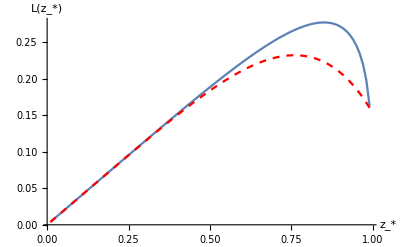

```mathematica
Show[ListLinePlot[Table[{zs,L[zs]/π},{zs,0.01,0.99,0.01}]],ListLinePlot[Table[{zs,L2[zs]/π},{zs,0.01,0.99,0.01}],PlotStyle->{Red,Dashed}],AxesLabel->{"z_*","L(z_*)"},PlotRange->All]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison_L(zs).pdf",%515,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison_L(zs).pdf

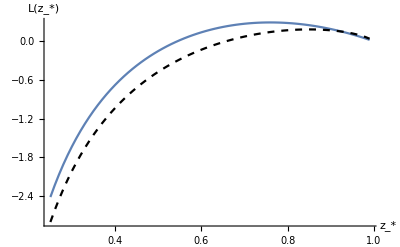

```mathematica
Show[ListLinePlot[Table[{zs,V2[zs]},{zs,0.25,0.99,0.01}]],ListLinePlot[Table[{zs,V[zs]},{zs,0.25,0.99,0.01}],PlotStyle->{Black,Dashed}],AxesLabel->{"z_*","L(z_*)"},PlotRange->All]
```

Check that width matches with original coordinates

Width matches, so far everything checks out.

Check potential w.r.t. width

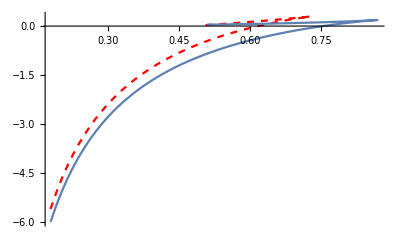

```mathematica
Show[ListLinePlot[Table[{L2[zs],V2[zs]},{zs,0.15,0.99,0.01}],PlotStyle->{Red,Dashed}],ListLinePlot[Table[{L[zs],V[zs]},{zs,0.15,0.99,0.01}],AxesLabel->{"L","V"}],PlotRange->All]
```

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison-V(L).pdf",%512,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison-V(L).pdf

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison-V(L).pdf",%508,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison-V(L).pdf

```mathematica
Export["/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison-V(L).pdf",%1348,"PDF"]
```

/home/htakko/Dropbox/Own/deep-learning-EE/figures/comparison-V(L).pdf

Good, also V(L) checks out.

```mathematica
Solve[y==(1-z)/(1-zs),z]
```

{{z→1-y+y zs}}

```mathematica
D[1-y+y zs,y]
```

-1+zs

```mathematica
Solve[y==√(1-z/zs),z]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z→zs-y^2 zs}}

```mathematica
D[zs-y^2 zs,y]
```

-2 y zs

### Integrals w.r.t. y=√(1-z/z_*)

```mathematica
L[zs_]:=4zs NIntegrate[((1-y^2)^2 √(f[zs]g[zs(1-y^2)]))/(√(f[zs(1-y^2)]-(1-y^2)^4 f[zs]))y,{y,0,1}]
V[zs_]:=4/zs NIntegrate[(√(f[zs(1-y^2)]g[zs(1-y^2)]))/((1-y^2)^2)(1/(√(1-((1-y^2)^4 f[zs])/f[zs(1-y^2)]))-1)y,{y,0,1}]-2NIntegrate[(√(f[z]g[z]))/z^2,{z,zs,1}]
```

Check with corrected x' (z):

Coordinate used in python says to be y = (1-z)/(1-zs)

```mathematica
Clear[g,f]
```

```mathematica
1/(√g[z] √(1-(z^4 f[zs]g[zs])/(zs^4 f[z]g[z])))/.z->zs-y^2 zs
```

1/(√(1-((zs-y^2 zs)^4 f[zs] g[zs])/(zs^4 f[zs-y^2 zs] g[zs-y^2 zs])) √g[zs-y^2 zs])

```mathematica
Clear[f,g]
```

```mathematica
(√(f[z]g[z]))/z^2(1/(√g[z] √(1-(z^4 f[zs]g[zs])/(zs^4 f[z]g[z])))-1)/.z->zs-y^2 zs//FullSimplify
```

((-1+1/(√(1-((-1+y^2)^4 f[zs] g[zs])/(f[zs-y^2 zs] g[zs-y^2 zs])) √g[zs-y^2 zs])) √(f[zs-y^2 zs] g[zs-y^2 zs]))/((zs-y^2 zs)^2)

```mathematica
L2[zs_]:=4NIntegrate[(zs y)1/(√g[zs-y^2 zs] √((zs^4 f[zs-y^2 zs] g[zs-y^2 zs])/((zs-y^2 zs)^4 f[zs] g[zs]))),{y,0,1}]
V2[zs_]:=4NIntegrate[(zs y)/((-1+y^2)^2 zs^2)(-√(f[zs-y^2 zs] g[zs-y^2 zs])+√(f[zs-y^2 zs] (g[zs-y^2 zs]+((-1+y^2)^4 f[zs] g[zs])/(g[zs-y^2 zs] (-(-1+y^2)^4 f[zs] g[zs]+f[zs-y^2 zs] g[zs-y^2 zs]))))),{y,0,1}]-2NIntegrate[(√(f[z]g[z]))/z^2,{z,zs,1}]
```

```mathematica
Clear[f,g]
```

```mathematica
4Integrate[D[((1-y^2)^2 √(f[zs]g[zs(1-y^2)]))/(√(f[zs(1-y^2)]-(1-y^2)^4 f[zs]))y,zs],{y,0,1}]//FullSimplify
```

4 ∫_0^1 ((y (-1+y^2)^2 (f[zs-y^2 zs] (g[zs-y^2 zs] f'[zs]-(-1+y^2) f[zs] g'[zs-y^2 zs])+f[zs] ((-1+y^2) g[zs-y^2 zs] f'[zs-y^2 zs]+(-1+y^2)^5 f[zs] g'[zs-y^2 zs])))/(2 (-(-1+y^2)^4 f[zs]+f[zs-y^2 zs])^(3/2) √(f[zs] g[zs-y^2 zs])))ⅆy

```mathematica
dLvanha[zs_]:=NIntegrate[4((y (-1+y^2)^2 (f[zs-y^2 zs] (g[zs-y^2 zs] f'[zs]-(-1+y^2) f[zs] g'[zs-y^2 zs])+f[zs] ((-1+y^2) g[zs-y^2 zs] f'[zs-y^2 zs]+(-1+y^2)^5 f[zs] g'[zs-y^2 zs])))/(2 (-(-1+y^2)^4 f[zs]+f[zs-y^2 zs])^(3/2) √(f[zs] g[zs-y^2 zs]))),{y,0,1}]
```

```mathematica
dL[zs_]:=4 NIntegrate[((y g[zs-y^2 zs] (zs f[zs-y^2 zs] g[zs] f'[zs]+f[zs] ((-1+y^2) zs g[zs] f'[zs-y^2 zs]+f[zs-y^2 zs] (2 g[zs]+zs g'[zs])))+2 y (-1+y^2) zs f[zs] f[zs-y^2 zs] g[zs] g'[zs-y^2 zs])/(2 (-1+y^2)^4 f[zs]^2 g[zs]^2 √g[zs-y^2 zs] ((f[zs-y^2 zs] g[zs-y^2 zs])/((-1+y^2)^4 f[zs] g[zs]))^(3/2))),{y,0,1}];
```

```mathematica
dL[0.99]
```

-0.585437

```mathematica
dLvanha[0.99]
```

-16.0026

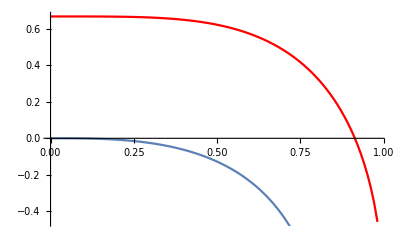

```mathematica
Show[ListLinePlot[Table[{zs,dL[zs]},{zs,0.001,0.99,0.01}],PlotStyle->Red],
ListLinePlot[Table[{zs,dLvanha[zs]},{zs,0.001,0.99,0.01}]]]
```

```mathematica
Clear[f,g]
```

```mathematica
D[4Integrate[(zs y)1/(√g[zs-y^2 zs] √((zs^4 f[zs-y^2 zs] g[zs-y^2 zs])/((zs-y^2 zs)^4 f[zs] g[zs]))),{y,0,1}],zs]//FullSimplify
```

4 ∫_0^1 ((y g[zs-y^2 zs] (zs f[zs-y^2 zs] g[zs] f'[zs]+f[zs] ((-1+y^2) zs g[zs] f'[zs-y^2 zs]+f[zs-y^2 zs] (2 g[zs]+zs g'[zs])))+2 y (-1+y^2) zs f[zs] f[zs-y^2 zs] g[zs] g'[zs-y^2 zs])/(2 (-1+y^2)^4 f[zs]^2 g[zs]^2 √g[zs-y^2 zs] ((f[zs-y^2 zs] g[zs-y^2 zs])/((-1+y^2)^4 f[zs] g[zs]))^(3/2)))ⅆy

```mathematica
L2[0.8]/π
```

0.153709

```mathematica
V2[0.8]
```

0.145518

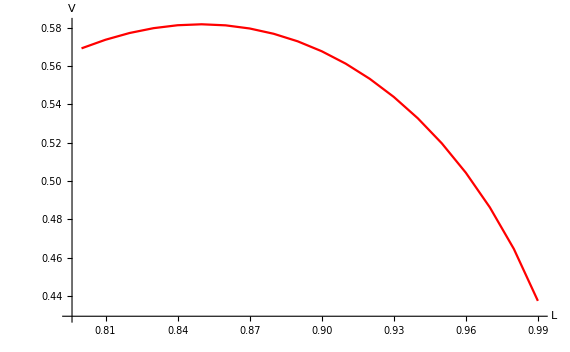

```mathematica
Show[ListLinePlot[Table[{zs,Vtest[zs]},{zs,0.8,0.99,0.01}],AxesLabel->{"L","V"},PlotStyle->{Red}]]
```

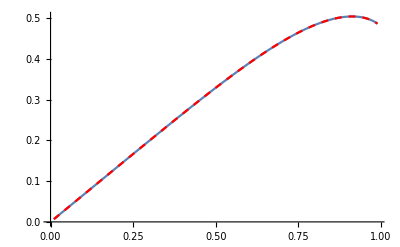

```mathematica
Show[ListLinePlot[Table[{zs,L2[zs]},{zs,0.01,0.99,0.01}]],ListLinePlot[Table[{zs,L2z[zs]},{zs,0.01,0.99,0.01}],PlotStyle->{Red,Dashed}]]
```

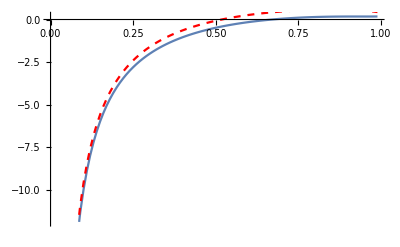

```mathematica
Show[ListLinePlot[Table[{zs,V2[zs]},{zs,0.01,0.99,0.01}]],ListLinePlot[Table[{zs,Vtest[zs]},{zs,0.01,0.99,0.01}],PlotStyle->{Red,Dashed}]]
```

## Alternative variables

### Integrals w.r.t. p

In the ρ-coordinate we defined the constant of motion
f(η_*)g(η_*)=(p_*)^2
and demanded that f(η)g(η)>(p_*)^2.
In the z-coordinate, the equivalent definition is
(f(z_*))/(z_*)^4=(p_*)^2
along with the demand that (f(z))/z^4>(p_*)^2.
In order to enforce this constraint, we simply choose to integrate w.r.t. p:=f(z)/z^4. Then

L=2∫_∞^(p_*) (p_*)/p(√(g(z)))/(√(1-(p_*)^2/p^2))z'(p)ⅆp 
V=2∫_∞^(p_*) p √(g(z))(1/(√(1-(p_*)^2/p^2))-1)z'(p)ⅆp-2∫_(p_*)^0 p √(g(z))z'(p)ⅆp  .

In AdS_5-BH, the relation between z<->p would be

```mathematica
z[p_]:=1/((1+p^2)^(1/4))
p[z_]:=(√f[z])/z^2
```

```mathematica
L[ps_]:=2NIntegrate[ps/p(√g[z[p]])/(√(1-ps^2/p^2))(-z'[p]),{p,ps,∞}]
V[ps_]:=2NIntegrate[p √g[z[p]](1/(√(1-ps^2/p^2))-1)(-z'[p]),{p,ps,∞}]-2NIntegrate[p √g[z[p]](-z'[p]),{p,0,ps}]
```

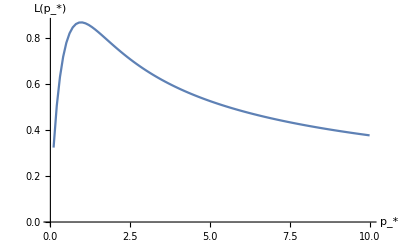

```mathematica
ListLinePlot[Table[{ps,L[ps]},{ps,0.1,10,0.1}],AxesLabel->{"p_*","L(p_*)"}]
```

```mathematica
Show[figV,ListLinePlot[Table[{L[ps],V[ps]},{ps,0.1,10,0.1}],AxesLabel->{"L","V"},PlotStyle->{Red,Dashed}]]
```

Show::gcomb: Could not combine the graphics objects in Show[figV,].

Show[figV,-Graphics-]

### Integrals w.r.t. y=√(1-(p_*)^2/p^2)

The above formulation still has the problem of having divergences in the integrands. For example, the L(p_*) integrand looks like

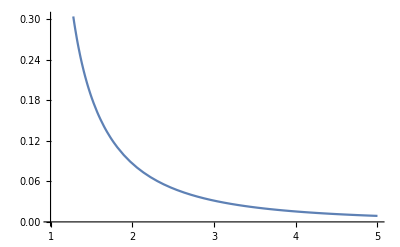

```mathematica
With[{ps=1},Plot[ps/p(√g[z[p]])/(√(1-ps^2/p^2))(-z'[p]),{p,ps,5ps}]]
```

Consider the change of variables
y=√(1-(p_*)/p)
p=(p_*)/(1-y^2) .
This has the advantage of killing off the divergences in the integrand and mapping the integration to y∈(0,1). Now the integrand looks like

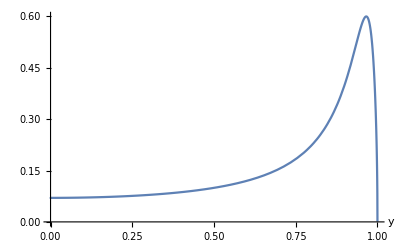

```mathematica
With[{ps=0.1},Plot[(1-y^2)(√g[z[ps/(1-y^2)]])/(√(1-(1-y^2)^2))(-z'[ps/(1-y^2)])(2 ps)/((1-y^2)^2)y,{y,0,1},AxesLabel->{"y"}]]
```

Much nicer. The integrals would now look like
L=4 p_*∫_0^1 y/(1-y^2)(√(g(z)))/(√(1-(1-y^2)^2))z'((p_*)/(1-y^2))ⅆy 
V=4(p_*)^2∫_0^1 y/((1-y^2)^3)√(g(z))(1/(√(1-(1-y^2)^2))-1)z'((p_*)/(1-y^2))ⅆy-2∫_(p_*)^0 p √(g(z))z'(p)ⅆp  .

```mathematica
L[ps_]:=4ps NIntegrate[-y/(1-y^2)(√g[z[ps/(1-y^2)]])/(√(1-(1-y^2)^2))z'[ps/(1-y^2)],{y,0,1}]
V[ps_]:=4 ps^2 NIntegrate[-y/((1-y^2)^3)√g[z[ps/(1-y^2)]](1/(√(1-(1-y^2)^2))-1)z'[ps/(1-y^2)],{y,0,1}]-2NIntegrate[p √g[z[p]](-z'[p]),{p,0,ps}]
```

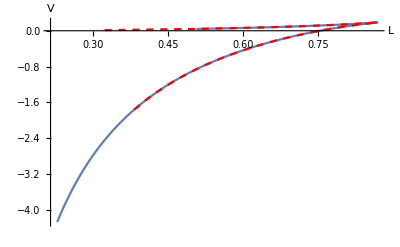

```mathematica
Show[figV,ListLinePlot[Table[{L[ps],V[ps]},{ps,0.1,10,0.1}],AxesLabel->{"L","V"},PlotStyle->{Red,Dashed}]]
```

V(L) still agrees with the original.

## Network parameters

Right now I’m leaning towards starting with everything in z and transforming to y=√(1-z/z_*). The plain integrals would be
L=4 z_*∫_0^1 (√(g(z)))/(√((f(z))/((1-y^2)^4 f(z_*))-1))yⅆy
S_NG-S_NG^(||)=(τ R^2)/(2π α')4/(z_*)∫_0^1 (√(f(z)g(z)))/((1-y^2)^2)(1/(√(1-((1-y^2)^4 f(z_*))/(f(z))))-1)yⅆy-2∫_(z_*)^1 (√(f(z)g(z)))/z^2 ⅆz
V= (S_NG-S_NG^(||))/τ,
where z=z_*(1-y^2).

Now we have to parametrize f(z) and g(z) somehow.

We’d like the parametrizations to be such that parameters have no constraints and AdS-BH corresponds to setting parameters to zero. Recall that our metric is defined
g=1/z^2(-f(z)d t^2+g(z)d z^2+d (x̄)^2) .

### f(z)

This should respect the constraints

Positive: f(z)>0

Asymptotically AdS_5: lim_(z→0) f(z)=1

Horizon at z=1: lim_(z→1) f(z)=0

Satisfy: ∂_z (f(z)/z^4)<0

AdS_5-BH would be f(z)=1-z^4, so we can try
f(z)=(1-z^4)/e^(a(z)),
where
a(z)=∫_0^z (a_1 x+a_2 x^2+...)^2 ⅆz .
This function is monotone, easy to evaluate and satisfies a(0)=0. f(z) is positive because of the exponential function. It is asymptotically AdS_5 because a(0)=0.

WHY is this a(z) to the power of 2???

```mathematica
Simplify[D[(1-z^4)/(Exp[a[z]] z^4),z]<0,0<z<1∧a[z]∈Reals∧a'[z]>0]
```

True

Monotonicity of f(z)/z^4 checks out.

```mathematica
Integrate[(a1 *x+a2*x^2)^2,{x,0,z}]
```

(a1^2 z^3)/3+1/2 a1 a2 z^4+(a2^2 z^5)/5

```mathematica
Simplify[(a1 z^2)/2+(a2 z^3)/3]
```

1/6 z^2 (3 a1+2 a2 z)

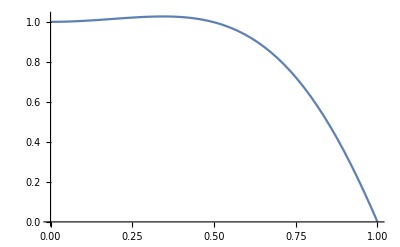

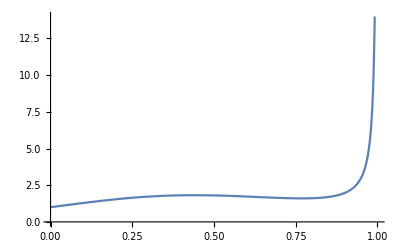

```mathematica
Plot[(1-z)*(1+z)*(1+z^2)/Exp[Integrate[(a1*x+a2*x^2),{x,0,z}]]/.a1->-1.1/.a2->1.8,{z,0,1}]
Plot[Exp[(b1*z-b2*z^2)]/((1-z)*(1+z)*(1+z^2))/.b1->2.9/.b2->3.7,{z,0,1},PlotRange->{{0,1},{0,14}}]
```

### g(z)

Positive: g(z)>0

Asymptotically AdS_5: lim_(z→0) g(z)=1

Horizon at z=1: lim_(z→1) g(z)=∞

In AdS_5-BH this would be g(z)=1/(1-z^4). A parameterization fulfilling these requirements would be
g(z)=ⅇ^(b(z))/(1-z^4),
where b(z) is an analytic function such that b(0)=0. Let’s try
b(z)=b_1 z+b_2 z^2+... .

### Joint constraints on f(z) and g(z)

We want the horizon temperature to be independent of parameters. The temperature is
T=1/(4π)√(f'(z)(1/(g(z)))')|_(z→1).

```mathematica
Simplify[1/(4π)√(D[(1-z^4)/Exp[a[z]],z]D[(1-z^4)/Exp[b[z]],z])/.z->1/.m[1]->1]
```

(√(ⅇ^(-a[1]-b[1])))/π

In order to remove the parameter dependence we must have a(1)+b(1)=0. This can always be satisfied when substitute this constraint into one of the parameters b_i. Let’s try
b(z)=b_1 z+b_2 z^2+...-(∑_i b_i+a(1))z^(N+1).